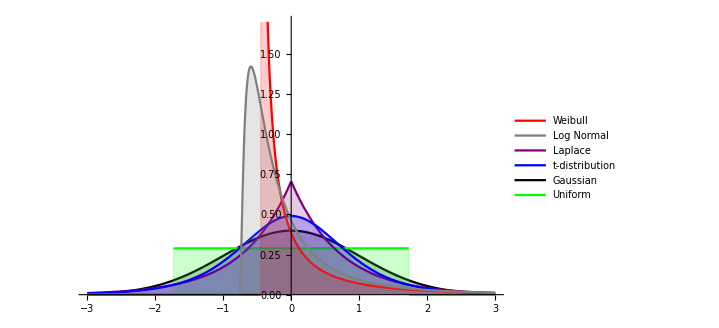

```mathematica
Show[{Plot[PDF[NormalDistribution[0, 1], x] // Evaluate,{x,-3,3}, Filling->Axis,PlotRange->{{-3, 3}, {0, 1.7}}, PlotStyle->Black ],
         Plot[PDF[UniformDistribution[{-√3, √3}], x] // Evaluate,{x,-3,3}, Filling->Axis,PlotRange->{{-3, 3}, {0, 1.7}}, PlotStyle->Green ],
         Plot[PDF[LaplaceDistribution[0, 1/(√2)], x] // Evaluate,{x,-3,3}, Filling->Axis,PlotRange->{{-3, 3}, {0, 1.7}}, PlotStyle->Purple ],
         Plot[PDF[StudentTDistribution[5], x * √5/3] *√5/3// Evaluate,{x,-3,3}, Filling->Axis,PlotRange->{{-3, 3}, {0, 1.7}}, PlotStyle->Blue ],
         Plot[PDF[WeibullDistribution[0.5,1] , 2 + x * √20]* √20//Evaluate,{x,-3,3}, Filling->Axis, PlotRange->{{-3, 3}, {0, 1.7}},  PlotStyle->Red],
         Plot[PDF[LogNormalDistribution[0.,1.] , √ⅇ + x * √(ⅇ*(ⅇ-1))]* √(ⅇ*(ⅇ-1))//Evaluate,{x,-3,3}, Filling->Axis,PlotRange->{{-3, 3}, {0, 1.7}}, PlotStyle->Gray,
                  PlotLegends -> LineLegend[{Red , Gray, Purple,  Blue, Black,Green},
                                                                      {"Weibull",  "Log Normal" , "Laplace", "t-distribution", "Gaussian", "Uniform"}]]
}]
```